```mathematica
d=2;
Rep={1,1.2,1.5,1.8,2,3,5,10};
RepResult={};
R[h_]:=d/4+h^2/d;
X[h_]:=(2R[h]-d)/2;
fr[theta_,R_]:=Abs[((R/4)Sin[2theta]-(2R-d)/2*Sqrt[(1-Cos[theta])/(1+Cos[theta])])]
Plot[{Maximize[{fr[theta,R[h]], 0<=theta<= 0.95ArcCos[X[h]/R[h]]},theta][[1]],fr[ArcCos[X[h]/R[h]],R[h]]},{h, d/2,5d},PlotRange->All,PlotTheme->"Scientific",Filling->Axis,PlotLabels->{"Middle","Top"}]
Plot[(180/Pi)Limit[theta,Maximize[{fr[theta,R[h]], 0<theta<0.95ArcCos[X[h]/R[h]]},theta][[2]][[1]]],{h, d/2,5d},PlotRange->All,PlotTheme->"Scientific",PlotStyle->Red,Filling->Axis]
For[i=1,i≤8,i++,RepResult=Append[RepResult,{i,Rep[[i]],N[Max[{Maximize[{fr[theta,R[Rep[[i]]]], 0<=theta<= 0.95ArcCos[X[Rep[[i]]]/R[Rep[[i]]]]},theta][[1]],fr[ArcCos[X[Rep[[i]]]/R[Rep[[i]]]],R[Rep[[i]]]]}]]}]];
ExportString[RepResult,"Table"]
Export["D:\\Mathematica files\\Result.xlsx",RepResult]
```

Here is the relationship between maximum normal stress and the ratio of height to half width.
The orange line shows the maximum normal stress in the middle of the arch, while the blue one shows the normal stress in the top, i.e. conjunction of two parts of the arch.

-Graphics-

Here is the relationship between the angle when maximum normal stress in the middle is reached and the ratio of height to half width.

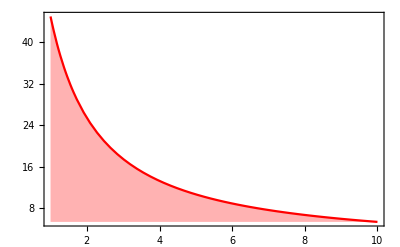

Here is the table showing maximum normal stress when height to half width varies. It is also exported to an Excel file. You can customize it to your local directory.

1	1	0.25
2	1.2	0.22043264647391464
3	1.5	0.1860226062117401
4	1.8	0.16014367239913685
5	2	0.15000000000000002
6	3	0.1333333333333333
7	5	0.09230769230769287
8	10	0.0490099009900975